# Lab 13: Double Integrals

### Instructions

Welcome to the assignment for the Double Integrals Lab. The purpose of this assignment is to assess your ability to find volumes using double integrals. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF. (Make sure you Rasterize all 3-dimensional plots)
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

Due Date:
see Canvas

### Question 1: Basic problems that you can verify without calculus to check your work.

a) The volume under the plane f(x,y)=5 over the rectangular region with 0≤x≤2 and 0≤y≤3 is shaped like a box with known volume. Set up a double integral to calculate this volume.

```mathematica
∫_0^3 ∫_0^2 5ⅆxⅆy
```

30

b) The volume under the plane f(x,y)=5 over the region shown below that is bounded by the x and y axes and the line y=-3/2x+3 should be half the volume of the object in the previous problem. Set up a double integral to calculate this volume.

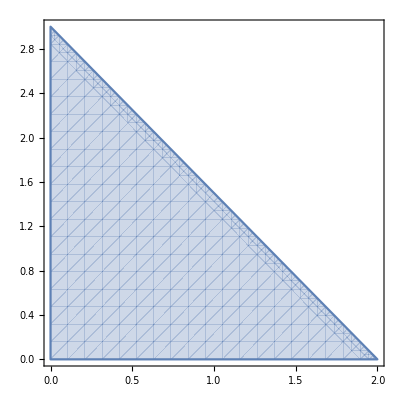

```mathematica
RegionPlot[0<x<2&&0<y<-3/2 x+3,{x,0,2},{y,0,3}]
```

```mathematica
∫_0^2 ∫_0^(-3/2x+3) 5ⅆyⅆx
```

15

### Question 2

a) Use the RegionPlot command to plot the area of a circle that is in the first quadrant (x>0 and y>0) given that the circle has a radius of 3 and is centered at the origin.  Your plot should use a range of -1 to 4 for both x and y values.  (Note: Your graph should be 1/4 of a circle).

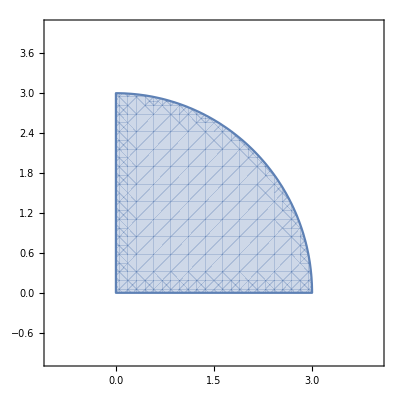

```mathematica
RegionPlot[0<y<√(9-x^2)&&0<x<3,{x,-1,4},{y,-1,4}]
```

b) Use the RegionPlot3D command to show the volume under z=√(9-x^2-y^2) but above the region in part "a".  Your plot should use a range of -1 to 4 for x, y, and z values. Note this should be 1/8 of a sphere with radius 3.

```mathematica
RegionPlot3D[0<y<√(9-x^2)&&0<x<3&&0<z<√(9-x^2-y^2),{x,-1,4},{y,-1,4},{z,-1,4},AxesLabel->{x,y,z},PlotPoints->100]//Rasterize
```

Less::nord: Invalid comparison with 0.+0.494021 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

-Graphics-

c) Set up a double integral to calculate the volume of the shape in part "b".

```mathematica
∫_0^3 ∫_0^(√(9-x^2)) √(9-x^2-y^2)ⅆyⅆx
```

(9 π)/2